{a→0.0947677,b→0.0416802,c→-0.0069467}

{0.0947677,0.0416802,-0.0069467}

0.0947677+0.0416802 x-0.0069467 x^2

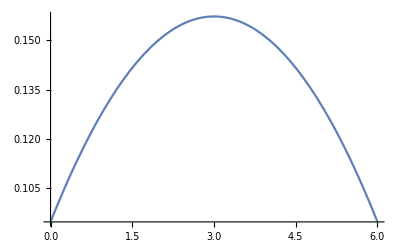

```mathematica
a=0;b=6;n=10;
h=(b-a)/n;
XDT={}; YDT={};
For[i=0,i≤n,i++, xdata[i]=N[a+i*h];ydata[i]=N[1/(2π)*Exp[-1/18(xdata[i])^2+1/3(xdata[i])-1/2]]; XDT=Append[XDT, xdata[i]];YDT=Append[YDT, ydata[i]];];
Clear[a,b,c,p,x];
p[a_,b_,c_,x_]:=a+b*x+c*x^2
eqn1=∑_(i=0)^n D[(p[a,b,c,xdata[i]]-ydata[i])^2, a]==0;
eqn2=∑_(i=0)^n D[(p[a,b,c,xdata[i]]-ydata[i])^2, b]==0;
eqn3=∑_(i=0)^n D[(p[a,b,c,xdata[i]]-ydata[i])^2, c]==0;
{eqn1, eqn2, eqn3}=Simplify[{eqn1, eqn2, eqn3}];
result=NSolve[{eqn1, eqn2, eqn3},{a,b,c}];
rules=Flatten[result]
{a,b,c}={a,b,c}/.rules
p[a,b,c,x]
Plot[p[a,b,c,x],{x,0,6}]
```